{A→-5.21041,B→1.71914}

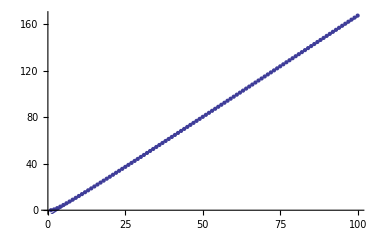

5.57974

0.00545943

```mathematica
SI={1};
For[n=2,n≤100,n++,
SIN=SI[[n-1]] + Sum[SI[[A]] SI[[n-A]],{A,1,n-1}];
AppendTo[SI,SIN];
];
SILog=Table[{n,Log[SI[[n]]]},{n,1,100}];
FFF=FindFit[SILog,A+B x,{A,B},x];
Print[FFF];
GrA=ListPlot[SILog];
GrB=Plot[(A+B x)/.FFF,{x,1,100}];
Show[GrA,GrB]
N[Exp[B]/.FFF]
N[Exp[A]/.FFF]
```

```mathematica
cc0=5.579739159925494;
NN0=0.005459430858665506;
cc=7.0;
Nmin=NN0(cc0/cc)/(1-cc0/cc);
Print[Nmin]
```

0.0214483